```mathematica
Generic Local Unitarity Supergraph Analyzer
```

```mathematica
Quit[]
```

## Resources

TODO read the info below from the supergraph once it will be available!

```mathematica
PDGtoMasses=Association[Join[Table[i->0,{i,-5,-1}],Table[i->0,{i,1,5}],{22->0,25->125.,21->0,6->173.,-6->173.}]];
```

### Supergraph and environment setup

```mathematica
RustBindingsPath="/Users/vjhirsch/MG5/3.0.2.py3/PLUGIN/aL_deformation/Mathematica";
AlphaLoopPath="/Users/vjhirsch/MG5/3.0.2.py3/PLUGIN/aL_deformation";
PythonBinaryPath="/opt/local/Library/Frameworks/Python.framework/Versions/3.9/bin/python3";
```

```mathematica
Get[RustBindingsPath<>"/"<>"RustFromMathematicaV2.m"]
```

Package for accessing alphaLoop implementation in Rust.
This V2 version uses the faster approach of StartExternalSession[Python] to talk to alphaLoop.

Variables you may want to overwrite are:

RFM$LTDFolder = <Path>;
RFM$PythonInterpreter = <Path>;
RFM$CUBAPath = <Path>;
RFM$SCSPath=<Path>;
RFM$ECOSPath=<Path>;

The function: 
RFM$GetLTDHook[name_,OptionsPattern[
{
RunMode->'LTD',
HyperparametersPath->'LTD/hyperparameters.yaml',
TopologiesPath->'LTD/topologies.yaml',
AmplitudesPath->'LTD/anplitudes.yaml',
DEBUG->False
}

Allows you to generate a hook, which will automatically be placed in the list:

RFM$AllHooksStarted

Then you can test that one hook is active with:

RFM$CheckHookStatus[hook_]

And use them to access information from Rust with the following three API entry points (for now):

RFM$GetLTDDeformation[hook_, RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$GetCrossSectionDeformation[hook_, CutID_,RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$GetRescaling[hook_, CutID_,RealMomenta_,OptionsPattern[DEBUG->False]]
RFM$Parameterize[hook_,LoopIndex_,ECM_,Xs_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$InvParameterize[hook_,LoopIndex_,ECM_,Momentum_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$Evaluate[hook_,Momenta_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$EvaluateCut[hook_,CutID_,scalingFactor_, scalingFactorJacobian_,Momenta_,OptionsPattern[{DEBUG->False,f128->False}]]
RFM$EvaluateIntegrand[hook_,Xs_,OptionsPattern[{DEBUG->False,f128->False}]]

Set your environment variables as follows:

RFM$CUBAPath = "<PATHTO>/Cuba-4.2/lib";
RFM$SCSPath="<PATHTO>/scs/out";
RFM$ECOSPath="<PATHTO>/ecos";
RFM$DYLDPATHS=RFM$CUBAPath<>":"<>RFM$SCSPath<>":"<>RFM$ECOSPath;

and then call:
RFM$SetEnvironment[];

Specify the running process path. It can be generated with the following command:

python3.7 ./bin/mg5_aMC --mode=global_dampening generate_epem_a_httx_NNLO_SG_QG_182.aL

import model aL_sm-no_widths
set_alphaLoop_option perturbative_orders {‘QCD’:4}
set_alphaLoop_option n_rust_inputs_to_generate -1
set_alphaLoop_option include_self_energies_from_squared_amplitudes True
set_alphaLoop_option differentiate_particle_from_antiparticle_in_graph_isomorphism False
set_alphaLoop_option consider_vertex_id_in_graph_isomorphism False
set_alphaLoop_option consider_edge_orientation_in_graph_isomorphism False
set_alphaLoop_option FORM_processing_output_format c
set_alphaLoop_option FORM_compile_arg all
set_alphaLoop_option apply_graph_isomorphisms True
set_alphaLoop_option qgraf_template_model epem
set_FORM_option number_of_lmbs None

set_alphaLoop_option FORM_compile_cores 32
set_FORM_option cores 32

set_alphaLoop_option qgraf_model SM_no_aqq
set_FORM_option generate_integrated_UV_CTs True
set_FORM_option generate_renormalisation_graphs False
set_alphaLoop_option FORM_compile_optimization 3
set_alphaLoop_option FORM_integrand_type both
set_FORM_option generate_arb_prec_output True
set_FORM_option on_shell_renormalisation True

set_alphaLoop_option SG_name_list [“SG_QG182”,]
set_FORM_option reference_lmb {“SG_QG182”:[“pq4”,”pq7”,”pq10”,“pq13”],}
qgraf_define j = d d~ g gh gh~
qgraf_generate e+ e- > a > h t t~ / u s c b QCD^2==2 QED^2==3 [QCD QCD]
#!rm -rf epem_a_httx_NNLO_SG_QG182
output qgraf epem_a_httx_NNLO_SG_QG182

but making sure you have p_1^μ=(500,0,0,500), p_2^μ=(500,0,0,-500) and thus Q^μ=(1000,0,0,0)

```mathematica
ProcessPath="/Users/vjhirsch/MG5/3.0.2.py3/epem_a_httx_NNLO_SG_QG182";
```

Specify the LTD folder to the hook package:

```mathematica
RFM$LTDFolder=AlphaLoopPath;
```

Also specify here your additional dependencies for the libraries alphaLoop depends on

```mathematica
RFM$CUBAPath = "/Users/vjhirsch/HEP_programs/Cuba-4.2/lib";
RFM$SCSPath="/Users/vjhirsch/MG5/3.0.2.py3/PLUGIN/aL_deformation/libraries/scs/out";
RFM$ECOSPath="/Users/vjhirsch/MG5/3.0.2.py3/PLUGIN/aL_deformation/libraries/ecos";
RFM$MPPPath="/Users/vjhirsch/HEP_programs/mppp/mppp_build/lib";
RFM$DYLDPATHS=RFM$CUBAPath<>":"<>RFM$SCSPath<>":"<>RFM$ECOSPath<>":"<>RFM$MPPPath;
RFM$SetEnvironment[]
```

```mathematica
(*
SetEnvironment["PATH"->Environment["PATH"]<>";"<>PythonBinaryPath];
RegisterExternalEvaluator["Python",PythonBinaryPath];
FindExternalEvaluators["Python"]
*)
```

Now create the hyperparameters file of interest

```mathematica
PY3session=StartExternalSession["Python"];
```

```mathematica
NoDeformationHyperparams = ResourceFunction["ImportYAML"][PY3session,NotebookDirectory[]<>"no_deformation.yaml"];
```

```mathematica
WithDeformationHyperparams = ResourceFunction["ImportYAML"][PY3session,NotebookDirectory[]<>"with_deformation.yaml"];
```

### Generic package functions

Clean monofont print with Sleep safety

```mathematica
MyPrint[msg_]:=Block[{},Pause[0.1];Print[Style[msg,FontFamily->"Monaco"]]]
ToStringFloat[flt_]:=If[ListQ[flt],
Table[ToStringFloat[f],{f,flt}],
If[NumberQ[flt],
ToString[If[Im[flt]==0,
Style[If[flt>=0,"+","-"]<>ToString[FortranForm[Abs[flt]]],FontFamily->"Monaco"],
Style[ToString[FortranForm[flt]],FontFamily->"Monaco"]
]],
flt]]
MyDataset[ds_,OptionsPattern[DatasetTheme->"Scientific"] ]:=Dataset[ds,DatasetTheme->OptionValue[DatasetTheme],ItemDisplayFunction->{#&,ToStringFloat[#]&}]
SafeLog10[x_]:=If[x!=0,Log10[x],0];
```

Get the hook to various deformation functional choices

First clean up all existing ones

```mathematica
GetHook[processPath_,yamlPath_,OptionsPattern[{hyperparameters->"hyperparameters.yaml",DEBUG->False}]]:=Block[{},
RFM$GetLTDHook[yamlPath,
RunMode->"cross_section",
HyperparametersPath->OptionValue[hyperparameters],
DEBUG->OptionValue[DEBUG],
MGNumeratorPath->processPath
]
]
```

```mathematica
RefreshHooks[]:=Module[{},
RFM$KillAllHooks[];
HookWithDeformation=GetHook[ProcessPath,ProcessPath<>"/Rust_inputs/SG_QG182.yaml",
hyperparameters->NotebookDirectory[]<>"/with_deformation.yaml"];
HookWithoutDeformation=GetHook[ProcessPath,ProcessPath<>"/Rust_inputs/SG_QG182.yaml",
hyperparameters->NotebookDirectory[]<>"no_deformation.yaml"];
{
RFM$CheckHookStatus[HookWithDeformation],
RFM$CheckHookStatus[HookWithoutDeformation]
}
]
```

```mathematica
SetMomenta[edgeMomenta_,SGYaml_,paramsYaml_,OptionsPattern[{MomentumPadding->Automatic,DEBUG->False,Seed->Automatic}]]:=Module[
{validLMBs,selectedLMB,externalMomenta,rotMatrix, shifts,LMBMomenta,MomentaInSelectedLMB,ECM,momPadding,momPaddingIndex=0},
validLMBs=Select[SGYaml["multi_channeling_lmb_bases"],
Function[lmbSpec,AllTrue[Keys[edgeMomenta],MemberQ[lmbSpec["defining_propagators"],#]&]]
];
If[
Length[validLMBs]==0,
MyPrint["Could not find a valid LMB for the following specified momenta: "<>ToString[Keys[edgeMomenta]]];
Return[Null];
];
selectedLMB=validLMBs⟦1⟧;
If[OptionValue[DEBUG],MyPrint["Selected LMB: "<>ToString[selectedLMB["defining_propagators"]]]];
ECM=Total[NoDeformationHyperparams["CrossSection"]["incoming_momenta"]]⟦1⟧;
momPadding=If[OptionValue[MomentumPadding]===Automatic,
{},OptionValue[MomentumPadding]
];
If[Not[OptionValue[Seed]===Automatic],SeedRandom[OptionValue[Seed]];];
momPadding=Join[
momPadding,
Table[Table[
ECM RandomReal[]
(*N[ECM((j+3 i+1)/(3(Length[selectedLMB["defining_propagators"]]-Length[edgeMomenta]-Length[momPadding])))]*)
,
{j,0,2}],{i,0,Length[selectedLMB["defining_propagators"]]-Length[edgeMomenta]-Length[momPadding]-1 }]
];
externalMomenta=Table[p⟦2;;⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}];
rotMatrix=Inverse[Table[selectedLMB["signatures"]⟦definingEdgeIndex⟧⟦1⟧,{definingEdgeIndex, Length[selectedLMB["defining_propagators"]]}]];
shifts=Table[selectedLMB["signatures"]⟦definingEdgeIndex⟧⟦2⟧,{definingEdgeIndex, Length[selectedLMB["defining_propagators"]]}].externalMomenta;
If[OptionValue[DEBUG],MyPrint["Rotation matrix to map to LMB: "<>ToString[rotMatrix]]];
If[OptionValue[DEBUG],MyPrint["Shifts to map to LMB: "<>ToString[shifts]]];
MomentaInSelectedLMB=Table[
If[MemberQ[Keys[edgeMomenta],edgeName],edgeMomenta[edgeName],momPaddingIndex++;momPadding⟦momPaddingIndex⟧]
,{edgeName,selectedLMB["defining_propagators"]}];
If[OptionValue[DEBUG],MyPrint["Momenta in selected LMB: "<>ToString[MomentaInSelectedLMB]]];
LMBMomenta=rotMatrix.(MomentaInSelectedLMB-shifts);
If[OptionValue[DEBUG],MyPrint["Momenta mapped to LMB: "<>ToString[LMBMomenta]]];
LMBMomenta
]
```

```mathematica
SetMomentaAssoc[edgeMomenta_,SGYaml_,paramsYaml_,OptionsPattern[{MomentumPadding->Automatic,DEBUG->False,Seed->Automatic}]]:=Module[{lmbMoms},
lmbMoms=SetMomenta[edgeMomenta,SGYaml,paramsYaml,MomentumPadding->OptionValue[MomentumPadding],DEBUG->OptionValue[DEBUG],Seed->OptionValue[Seed]];
Association[Table[SGYaml["loop_momentum_basis"]⟦iLMB⟧->lmbMoms⟦iLMB⟧,{iLMB,Length[SGYaml["loop_momentum_basis"]]}]]
]
```

```mathematica
GetDeformation[hook_,cutID_,momentaInLMB_,SGYaml_,paramsYaml_,OptionsPattern[{DEBUG->False}]]:=Module[
{ECM, rescaling,rescalingJac, deformationRes,cbTOlmbMatrix},
rescaling=RFM$GetRescaling[hook,cutID,momentaInLMB];
If[OptionValue[DEBUG],MyPrint["Rescalings for cut #"<>ToString[cutID]<>" : "<>ToString[rescaling]]];
If[Or[Length[rescaling["tSolutions"]]!=2,rescaling["tSolutions"]⟦2⟧<=0.],
MyPrint["ERROR: Could not find t-scaling for cut #"<>ToString[cutID]<>"the following edge momenta config: "<>ToString[momentaInLMB]];
Return[Null];
];
rescalingJac=rescaling["tJacobians"]⟦2⟧;
rescaling=rescaling["tSolutions"]⟦2⟧;
deformationRes=RFM$GetCrossSectionDeformation[hook,cutID,rescaling,momentaInLMB];
deformationRes["DeformedMomenta"]=Table[Table[dmi⟦2⟧,{dmi,dm⟦2;;⟧}],{dm,deformationRes["DeformedMomenta"]}];
cbTOlmbMatrix=SGYaml["cutkosky_cuts"]⟦cutID+1⟧["diagram_sets"]⟦1⟧["cb_to_lmb"];
cbTOlmbMatrix=Table[ cbTOlmbMatrix⟦i;;i+3⟧,{i,1,Length[cbTOlmbMatrix],4}];
deformationRes["DeformedMomenta"]=cbTOlmbMatrix.deformationRes["DeformedMomenta"];
<|
"MomentaDeformationInLMB"->deformationRes["DeformedMomenta"],
"DeformationJacobian"->deformationRes["DeformationJacobian"]
|>
]
```

```mathematica
EvaluatePoint[
hook_,edgeMomenta_,SGYaml_,paramsYaml_,OptionsPattern[{MomentumPadding->Automatic,DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,Seed->Automatic,Esurfaces->Null}]
]:=Module[
{MomentaInLMB,MomentaInLMBAssoc,ComplexMomentaInLMBAssoc, DeformationInLMB,rescaling,rescalingJac,invXsMap,resForCut,deformationRes,
cbTOlmbMatrix,cutResults,ECM,TotalInvJacobian,integrandEval,finalRes,completeResForCut,deformationDirection,tmpA},
MomentaInLMB=SetMomenta[edgeMomenta,SGYaml,paramsYaml,MomentumPadding->OptionValue[MomentumPadding],DEBUG->OptionValue[DEBUG],Seed->OptionValue[Seed]];
ECM=Total[NoDeformationHyperparams["CrossSection"]["incoming_momenta"]]⟦1⟧;

invXsMap=Table[RFM$InvParameterize[hook,iLMB-1,ECM^2,MomentaInLMB⟦iLMB⟧,f128->OptionValue[f128]],{iLMB,Length[MomentaInLMB]}];
TotalInvJacobian=Times@@Table[x["Jacobian"],{x,invXsMap}];
If[OptionValue[DEBUG],MyPrint["Total inverse Jacobian : "<>ToStringFloat[TotalInvJacobian]]];
integrandEval=RFM$EvaluateIntegrand[hook,Join@@Table[x["Xs"],{x,invXsMap}]];
If[OptionValue[DEBUG],MyPrint["Input xs for integrand eval call : "<>ToString[Join@@Table[x["Xs"],{x,invXsMap}]]]];
If[OptionValue[DEBUG],MyPrint["Result for integrand eval : "<>ToStringFloat[integrandEval]]];

If[Not[OptionValue[IncludeJacobian]],
integrandEval=integrandEval*TotalInvJacobian;
];
If[Not[OptionValue[Phase]===Null],
integrandEval=OptionValue[Phase][integrandEval];
];

cutResults=Table[
rescaling=RFM$GetRescaling[hook,iCut,MomentaInLMB];
If[OptionValue[DEBUG],MyPrint["Rescalings for cut #"<>ToString[iCut]<>" : "<>ToString[rescaling]]];
If[Or[Length[rescaling["tSolutions"]]!=2,rescaling["tSolutions"]⟦2⟧<=0.],
MyPrint["ERROR: Could not find t-scaling for cut #"<>ToString[iCut]<>"the following edge momenta config: "<>ToString[MomentaInLMB]];
Return[Null];
];
rescalingJac=rescaling["tJacobians"]⟦2⟧;
rescaling=rescaling["tSolutions"]⟦2⟧;
resForCut=RFM$EvaluateCut[hook,iCut,rescaling,rescalingJac,MomentaInLMB,f128->OptionValue[f128]];
If[OptionValue[DEBUG],MyPrint["Result for cut #"<>ToString[iCut]<>" : "<>ToStringFloat[resForCut]]];
If[OptionValue[IncludeJacobian],
resForCut=resForCut/TotalInvJacobian;
];
If[Not[OptionValue[Phase]===Null],
resForCut=OptionValue[Phase][resForCut];
];
deformationRes=RFM$GetCrossSectionDeformation[hook,iCut,rescaling,MomentaInLMB];
deformationRes["DeformedMomenta"]=Table[Table[dmi⟦2⟧,{dmi,dm⟦2;;⟧}],{dm,deformationRes["DeformedMomenta"]}];
cbTOlmbMatrix=SGYaml["cutkosky_cuts"]⟦iCut+1⟧["diagram_sets"]⟦1⟧["cb_to_lmb"];
cbTOlmbMatrix=Table[ cbTOlmbMatrix⟦i;;i+3⟧,{i,1,Length[cbTOlmbMatrix],4}];
deformationRes["DeformedMomenta"]=cbTOlmbMatrix.deformationRes["DeformedMomenta"];

completeResForCut=<|
"edges"->AlphabeticSort[Table[c["name"],{c,SGYaml["cutkosky_cuts"]⟦iCut+1⟧["cuts"]}]],
"Res"->resForCut ,
"Rescaling"->rescaling ,
"MomentaInLMB"->MomentaInLMB,
"MomentaDeformationInLMB"->deformationRes["DeformedMomenta"],
"DeformationJacobian"->deformationRes["DeformationJacobian"]
|>;

If[
Not[OptionValue[Esurfaces]===Null],
MomentaInLMBAssoc=Association[Table[SGYaml["loop_momentum_basis"]⟦iLMB⟧->rescaling MomentaInLMB⟦iLMB⟧,{iLMB,Length[MomentaInLMB]}]];
ComplexMomentaInLMBAssoc=Association[Table[SGYaml["loop_momentum_basis"]⟦iLMB⟧->(rescaling MomentaInLMB⟦iLMB⟧+ⅈ deformationRes["DeformedMomenta"]⟦iLMB⟧),{iLMB,Length[MomentaInLMB]}]];
completeResForCut=AssociateTo[completeResForCut,
Flatten[Table[{
{cat,"Esurf analysis"}->SortBy[Table[
deformationDirection=(
Table[es["GradEq"]⟦iLMB⟧.deformationRes["DeformedMomenta"]⟦iLMB⟧,{iLMB,Length[SGYaml["loop_momentum_basis"]]}]
)/.GenerateLoopMomenta[SGYaml,moms->MomentaInLMBAssoc];
tmpA=Total[Table[Norm[es["GradEq"]⟦iLMB⟧]Norm[deformationRes["DeformedMomenta"]⟦iLMB⟧],{iLMB,Length[SGYaml["loop_momentum_basis"]]}]];
Association[{
"id"->es["id"],
"edges"->Table[AlphabeticSort[enames],{enames,es["edgeNames"]}],
"eval"->(es["Eq"]/ECM)/.GenerateLoopMomenta[SGYaml,moms->MomentaInLMBAssoc],
"complex eval"->(es["Eq"]/ECM)/.GenerateLoopMomenta[SGYaml,moms->ComplexMomentaInLMBAssoc],
"Normalised κ⃗.∇_(k⃗) η(k⃗)"->If[tmpA!=0,Total[deformationDirection]/tmpA,0.]
}],{es,OptionValue[Esurfaces][cat]}],
(Abs[#["eval"]])&
]
},
{cat,{"s-channel","soft"}}
]]
];
];

completeResForCut
,{iCut,0,Length[SGYaml["cutkosky_cuts"]]-1}
];

finalRes=Association[Join[
Table[(iCut-1)->cutResults⟦iCut⟧,{iCut,Length[cutResults]}],
{
"CutsSum"-><|"Res"->Total[Table[cr["Res"],{cr,cutResults}]]|>,
"FullIntegrand"-><|"Res"->integrandEval|>
}
]];

finalRes

]
```

```mathematica
DisplayEvaluationEsurf[allEvals_,SGYaml_,OptionsPattern[Categories->{"s-channel","soft"}]]:=Module[
{},
Table[
Print[StringJoin[Table["-",{i,Range[50]}]]];
Print["Analysis of "<>cat<>" E-surfaces:"];
Print[StringJoin[Table["-",{i,Range[50]}]]];
Print[Table[
{
{"Cut #"<>ToString[iCut],AlphabeticSort[Table[c["name"],{c,SGYAMLinfo["cutkosky_cuts"]⟦iCut+1⟧["cuts"]}]]}//Multicolumn[#,2]&,
MyDataset[evaluationWithEsurfaceAnalysis[iCut][{cat,"Esurf analysis"}]]
}//Multicolumn[#,1]&
,{iCut,0,Length[SGYAMLinfo["cutkosky_cuts"]]-1}]//Multicolumn[#,2]&
];
,
{cat,OptionValue[Categories]}];
]
```

```mathematica
ComputeAllMomenta[lmbMomentaAssoc_,SGYaml_,paramsYaml_,OptionsPattern[DatasetOutput->False]]:=Module[
{externalMomenta,res,lmbMomenta},
lmbMomenta=Table[lmbMomentaAssoc[em],{em,SGYaml["loop_momentum_basis"]}];
externalMomenta=Table[p⟦2;;⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}];
res=Association[Table[k->(
 SGYaml["edge_signatures"][k]⟦1⟧.lmbMomenta+
SGYaml["edge_signatures"][k]⟦2⟧.externalMomenta
),{k,AlphabeticSort[Keys[SGYaml["edge_signatures"]]]}]];
If[Not[OptionValue[DatasetOutput]],
res,
MyDataset[
Association[
Table[
k->Association[{"p_x"->res[k]⟦1⟧,"p_y"->res[k]⟦2⟧,"p_z"->res[k]⟦3⟧}],
{k,AlphabeticSort[Keys[res]]}
]
]
]
]
]
```

```mathematica
AnalyzeApproach[hook_,edgeMomenta_,SGYaml_,paramsYaml_,OptionsPattern[{MomentumPadding->Automatic,DEBUG->False,f128->True,Phase->Null,IncludeJacobian->False,Phase->Null,NPoints->10,ApproachSide->1,ApproachDirections->Automatic,Seed->Automatic, LambdaMax->12.,LambdaMin->0}]
]:=Module[
{approachDirections,furtherSeed,ECM,lambdas,edgeMomsForThisLambda,allResults},
ECM=Total[NoDeformationHyperparams["CrossSection"]["incoming_momenta"]]⟦1⟧;
If[Not[OptionValue[Seed]===Automatic],SeedRandom[OptionValue[Seed]];];
furtherSeed=RandomInteger[{1,1000}];
approachDirections=If[OptionValue[ApproachDirections]===Automatic,
<||>,OptionValue[ApproachDirections]];
Table[
If[Not[MemberQ[Keys[approachDirections],em]],
AssociateTo[approachDirections,em->Table[ECM RandomReal[],{j,3}]];
];
,{em,Keys[edgeMomenta]}];
lambdas=Table[10^-l,{l,OptionValue[LambdaMin],OptionValue[LambdaMax],(OptionValue[LambdaMax]-OptionValue[LambdaMin])/OptionValue[NPoints]}];
allResults=Table[
edgeMomsForThisLambda=Association[Table[
e->(edgeMomenta[e]+lambda*OptionValue[ApproachSide]*approachDirections[e])
,{e,Keys[edgeMomenta]}]];
{lambda,EvaluatePoint[
hook,edgeMomsForThisLambda,SGYaml,paramsYaml,Seed->furtherSeed,
DEBUG->OptionValue[DEBUG],f128->OptionValue[f128],IncludeJacobian->OptionValue[IncludeJacobian],Phase->OptionValue[Phase]
]}
,{lambda,lambdas}];

allResults
]
```

```mathematica
MonitorApproachResult[rawResults_,SGYaml_,paramsYaml_,OptionsPattern[{cuts->All,ApproachSide->1,SelectedImageSize->1000,IntegrandToPlot->(SafeLog10[Abs[Re[#]]]&)}]]:=Module[{dataToPlot,IntegrandToPlotFunction,plotRange,selectedCuts,selectedCutsNoSum,scalings,scalingEntries},

selectedCuts=Table[iCut,{iCut,-1,Length[SGYaml["cutkosky_cuts"]]-1}];
If[Not[OptionValue[cuts]===All],selectedCuts=Select[selectedCuts,MemberQ[OptionValue[cuts],#]&];];
selectedCutsNoSum=Select[selectedCuts,Not[#==-1]&];
scalingEntries={Round[Length[rawResults]*0.8],Round[Length[rawResults]*0.9]};
{
(* Integrand plots *)
{
dataToPlot = Join[
If[MemberQ[selectedCuts,-1],{Table[{-Sign[OptionValue[ApproachSide]]SafeLog10[r⟦1⟧],OptionValue[IntegrandToPlot][r⟦2⟧["FullIntegrand"]["Res"]]},{r,rawResults}]},{}],
Table[
Table[{-Sign[OptionValue[ApproachSide]]SafeLog10[r⟦1⟧],OptionValue[IntegrandToPlot][r⟦2⟧[iCut]["Res"]]},{r,rawResults}]
,{iCut,selectedCutsNoSum}]
];
scalings=Association[Table[selectedCuts⟦i⟧->Round[-(Abs[dataToPlot⟦i⟧⟦scalingEntries⟦1⟧⟧⟦2⟧]-Abs[dataToPlot⟦i⟧⟦scalingEntries⟦2⟧⟧⟦2⟧])/(Abs[dataToPlot⟦i⟧⟦scalingEntries⟦1⟧⟧⟦1⟧]-Abs[dataToPlot⟦i⟧⟦scalingEntries⟦2⟧⟧⟦1⟧]),0.001],{i,Length[selectedCuts]}]];
plotRange={Min[Table[Min[Table[r⟦2⟧,{r,l}]],{l,dataToPlot}]],Max[Table[Max[Table[r⟦2⟧,{r,l}]],{l,dataToPlot}]]};
plotRange={plotRange⟦1⟧-(plotRange⟦2⟧-plotRange⟦1⟧)/5,plotRange⟦2⟧+(plotRange⟦2⟧-plotRange⟦1⟧)/5};
ListLinePlot[
dataToPlot
,
AxesLabel->{"10^-λ","F[I^(LU)]"},
PlotStyle->Join[If[MemberQ[selectedCuts,-1],{Thickness[0.004]},{}],Table[Thickness[0.002],{c,selectedCutsNoSum}]],
PlotLegends->Placed[
Join[If[MemberQ[selectedCuts,-1],{"Complete LU integrand (scaling: "<>ToString[scalings[-1]]<>" )"},{}],Table["Cut #"<>ToString[iCut]<>" : "<>StringRiffle[AlphabeticSort[Table[c["name"],{c,SGYaml["cutkosky_cuts"]⟦iCut+1⟧["cuts"]}]]]<>" (scaling: "<>ToString[scalings[iCut]]<>" )",{iCut,selectedCutsNoSum}]],
If[OptionValue[ApproachSide]>0,Left,Right]],
PlotRange->plotRange,
ImageSize->OptionValue[SelectedImageSize],
PlotStyle->Automatic,
PlotLabel->"Local Unitarity integrands, F=("<>ToString[OptionValue[IntegrandToPlot]]<>")"<>If[OptionValue[ApproachSide]>0,"( Left approach )","( Right approach) "]
]
},
(* Deformation plots *)
{
dataToPlot = Table[
Table[{-Sign[OptionValue[ApproachSide]]SafeLog10[r⟦1⟧],SafeLog10[Total[Table[Norm[κ],{κ,r⟦2⟧[iCut]["MomentaDeformationInLMB"]}]]]},{r,rawResults}]
,{iCut,selectedCutsNoSum}
];
scalings=Association[Table[selectedCutsNoSum⟦i⟧->Round[-(Abs[dataToPlot⟦i⟧⟦scalingEntries⟦1⟧⟧⟦2⟧]-Abs[dataToPlot⟦i⟧⟦scalingEntries⟦2⟧⟧⟦2⟧])/(Abs[dataToPlot⟦i⟧⟦scalingEntries⟦1⟧⟧⟦1⟧]-Abs[dataToPlot⟦i⟧⟦scalingEntries⟦2⟧⟧⟦1⟧]),0.001],{i,Length[selectedCutsNoSum]}]];
plotRange={Min[Table[Min[Table[r⟦2⟧,{r,l}]],{l,dataToPlot}]],Max[Table[Max[Table[r⟦2⟧,{r,l}]],{l,dataToPlot}]]};
plotRange={plotRange⟦1⟧-(plotRange⟦2⟧-plotRange⟦1⟧)/5,plotRange⟦2⟧+(plotRange⟦2⟧-plotRange⟦1⟧)/5};
ListLinePlot[
dataToPlot
,
AxesLabel->{"10^-λ","Log_10[|κ|]"},
PlotStyle->Table[Thickness[0.002],{c,SGYaml["cutkosky_cuts"]}],
PlotLegends->Placed[
Table["Cut #"<>ToString[iCut]<>" : "<>StringRiffle[AlphabeticSort[Table[c["name"],{c,SGYaml["cutkosky_cuts"]⟦iCut+1⟧["cuts"]}]]]<>" (scaling: "<>ToString[scalings[iCut]]<>" )",{iCut,selectedCutsNoSum}],
If[OptionValue[ApproachSide]>0,Left,Right]],
PlotRange->plotRange,
ImageSize->OptionValue[SelectedImageSize],
PlotStyle->Automatic,
PlotLabel->"Deformation magnitude"<>If[OptionValue[ApproachSide]>0,"( Left approach )","( Right approach) "]
]
}
}

]
```

```mathematica
DoubleSidedApproach[hook_,point_,SGYaml_,paramsYaml_,OptionsPattern[{MomentumPadding->Automatic,DEBUG->False,f128->True,Phase->Null,IncludeJacobian->False,Phase->Null,NPoints->10,ApproachDirections->Automatic,Seed->Automatic, LambdaMax->7.,LambdaMin->0}]]:=Module[
{approachLeft, approachRight},
approachLeft=AnalyzeApproach[
hook,point,SGYaml,paramsYaml,
MomentumPadding->OptionValue[MomentumPadding],DEBUG->OptionValue[DEBUG],f128->OptionValue[f128],Phase->OptionValue[Phase],NPoints->OptionValue[NPoints],
ApproachSide->1,IncludeJacobian->OptionValue[IncludeJacobian],ApproachDirections->OptionValue[ApproachDirections],Seed->OptionValue[Seed],
LambdaMax->OptionValue[LambdaMax],LambdaMin->OptionValue[LambdaMin]
];
approachRight=AnalyzeApproach[
hook,point,SGYaml,paramsYaml,
MomentumPadding->OptionValue[MomentumPadding],DEBUG->OptionValue[DEBUG],f128->OptionValue[f128],Phase->OptionValue[Phase],NPoints->OptionValue[NPoints],
ApproachSide->-1,IncludeJacobian->OptionValue[IncludeJacobian],ApproachDirections->OptionValue[ApproachDirections],Seed->OptionValue[Seed],
LambdaMax->OptionValue[LambdaMax],LambdaMin->OptionValue[LambdaMin]
];
<|"Left"->approachLeft,"Right"->approachRight|>
]
```

```mathematica
DoubleSidedMonitor[rawData_,SGYaml_,paramsYaml_,
OptionsPattern[{cuts->All,SelectedImageSize->600,IntegrandToPlot->(SafeLog10[Abs[Re[#]]]&)}]
]:=Module[{monitorLeft,monitorRight},
monitorLeft=MonitorApproachResult[rawData["Left"],SGYaml,paramsYaml,cuts->OptionValue[cuts],ApproachSide->1,SelectedImageSize->OptionValue[SelectedImageSize],IntegrandToPlot->OptionValue[IntegrandToPlot]];
monitorRight=MonitorApproachResult[rawData["Right"],SGYaml,paramsYaml,cuts->OptionValue[cuts],ApproachSide->-1,SelectedImageSize->OptionValue[SelectedImageSize],IntegrandToPlot->OptionValue[IntegrandToPlot]];
Table[
Join[monitorLeft⟦iRow⟧,monitorRight⟦iRow⟧],{iRow,Length[monitorLeft]}
]
]
```

```mathematica
GenerateLoopMomenta[SGYaml_,OptionsPattern[{moms->Null}]]:=Module[{loopMoms},
loopMoms=Table[Table[ToExpression["k"<>ToString[i]<>(<|1->"x",2->"y",3->"z"|>)[j]],{j,1,3}],{i,Length[SGYAMLinfo["loop_momentum_basis"]]}];
If[
OptionValue[moms]===Null,loopMoms,
Flatten[Table[Table[loopMoms⟦i⟧⟦j⟧->OptionValue[moms][SGYaml["loop_momentum_basis"]⟦i⟧]⟦j⟧,{j,1,3}],{i,1,Length[loopMoms]}]]
]
]
```

```mathematica
BuildESurfaceEquation[Esurf_,SGYaml_,paramsYaml_]:=Module[
{externalMomenta,externalMomentaEs,loopMoms,q,EsurfEq,edgesToMass},
If[And[Esurf["IncomingEdges"]===Null,Esurf["OutgoingEdges"]===Null],Return[<|"Eq"->Null,"GradEq"->Null|>];];

edgesToMass=Association[Table[e⟦1⟧->PDGtoMasses[e⟦2⟧],{e,SGYAMLinfo["edge_PDGs"]}]];
loopMoms=GenerateLoopMomenta[SGYaml];
externalMomenta=Chop[Table[p⟦2;;⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}],10^-15];
externalMomentaEs=Chop[Table[p⟦1⟧,{p,Join[paramsYaml["CrossSection"]["incoming_momenta"],paramsYaml["CrossSection"]["incoming_momenta"]]}],10^-15];
EsurfEq=Total[Table[
q=( SGYaml["edge_signatures"][eOUT]⟦1⟧.loopMoms+
SGYaml["edge_signatures"][eOUT]⟦2⟧.externalMomenta);
Sqrt[q.q+edgesToMass[eOUT]^2],
{eOUT,Esurf["OutgoingEdges"]}]]
-
If[Esurf["type"]=="s-channel",
Total[Table[
SGYaml["edge_signatures"][eIN]⟦2⟧.externalMomentaEs,
{eIN,Esurf["IncomingEdges"]}]],
Total[Table[
q=( SGYaml["edge_signatures"][eIN]⟦1⟧.loopMoms+
SGYaml["edge_signatures"][eIN]⟦2⟧.externalMomenta);
Sqrt[q.q+edgesToMass[eIN]^2],
{eIN,Esurf["IncomingEdges"]}]]
];
EsurfEq=Chop[EsurfEq,10^-20];

<|
"Eq"->EsurfEq,
"GradEq"->Table[Table[Simplify[D[EsurfEq,lme]],{lme,lm}],{lm,loopMoms}]
|>

]
```

```mathematica
FindPointOnEsurfaces[Esurfs_,SGYaml_,paramsYaml_,OptionsPattern[{AcceptThreshold->10^-16,DEBUG->False,QuietMode->False}]]:=Module[
{minimizeRes,loopMoms,ECM},
If[AnyTrue[Esurfs,(#["Eq"]===Null)&],Return[Null];];
ECM=Total[NoDeformationHyperparams["CrossSection"]["incoming_momenta"]]⟦1⟧;

loopMoms=GenerateLoopMomenta[SGYaml];
If[OptionValue[QuietMode],Quiet[
minimizeRes=NMinimize[
SetPrecision[1/ECM Total[Table[Es["Eq"]^2,{Es,Esurfs}]],(-Log10[OptionValue[AcceptThreshold]]+4)],Flatten[loopMoms],
PrecisionGoal->(-Log10[OptionValue[AcceptThreshold]]+2),AccuracyGoal->(-Log10[OptionValue[AcceptThreshold]]+2),WorkingPrecision->(-Log10[OptionValue[AcceptThreshold]]+2)
];
],
minimizeRes=NMinimize[
SetPrecision[1/ECM Total[Table[Es["Eq"]^2,{Es,Esurfs}]],(-Log10[OptionValue[AcceptThreshold]]+4)],Flatten[loopMoms],
PrecisionGoal->(-Log10[OptionValue[AcceptThreshold]]+2),AccuracyGoal->(-Log10[OptionValue[AcceptThreshold]]+2),WorkingPrecision->(-Log10[OptionValue[AcceptThreshold]]+2)
];
];
If[OptionValue[DEBUG],MyPrint["FindPointOnEsurfaces found the following solution with evaluation "<>ToStringFloat[minimizeRes⟦1⟧]<>" : "<>ToStringFloat[loopMoms/.minimizeRes⟦2⟧]]];
If[Abs[minimizeRes⟦1⟧]<OptionValue[AcceptThreshold],
Association[Table[SGYaml["loop_momentum_basis"]⟦lmi⟧->Chop[(loopMoms⟦lmi⟧/.minimizeRes⟦2⟧),10^-16 ECM],{lmi,Length[loopMoms]}]],{}
]
]
```

```mathematica
MapFromXs[hook_,xs_,SGYaml_,paramsYaml_,OptionsPattern[{basis->Automatic,f128->True}]]:=Module[
{riffledXs,momsMap,allMoms,ECM,selectedBasis},
ECM=Total[NoDeformationHyperparams["CrossSection"]["incoming_momenta"]]⟦1⟧;
selectedBasis=If[OptionValue[basis]===Automatic,SGYaml["loop_momentum_basis"],OptionValue[basis]];
riffledXs=Table[xs⟦iMom*3+1;;(iMom+1)*3⟧,{iMom,0,Length[SGYaml["loop_momentum_basis"]]-1}];

momsMap=Table[RFM$Parameterize[hook,iLMB-1,ECM^2,riffledXs⟦iLMB⟧,f128->OptionValue[f128]],{iLMB,Length[SGYaml["loop_momentum_basis"]]}];
SetMomentaAssoc[Association[Table[selectedBasis⟦iEdge⟧->momsMap⟦iEdge⟧["Momentum"],{iEdge,Length[SGYaml["loop_momentum_basis"]]}]],SGYaml,paramsYaml]
]
```

### Graph functions for supergraphs analysis

```mathematica
GetSuperGraph[SGYaml_,OptionsPattern[{ShowVertexLabels->None,Size->300}]]:=DirectedGraph[
Table[e⟦2⟧->e⟦3⟧,{e,SGYAMLinfo["topo_edges"]}
],
VertexLabels->OptionValue[ShowVertexLabels],
ImageSize->OptionValue[Size]
]
```

```mathematica
GenerateAllLMBs[SGYaml_,OptionsPattern[{DEBUG->False}]]:=Module[{g,spanningTrees},
g=GetSuperGraph[SGYaml];
spanningTrees=Select[TreeGraphQ[UndirectedGraph[#1]]&][Select[VertexCount[#1]==VertexCount[g]&][Subsets[EdgeList[g],{EdgeCount[g]-SGYAMLinfo["topo"]["n_loops"]}]]];
Table[DirectedGraph[Select[EdgeList[g],Function[e,Not[MemberQ[EdgeList[st],e]]]] ],{st,spanningTrees}]
]
```

```mathematica
GraphsMinusEsurface[embeddingGraph_,Esurf_,OptionsPattern[{IncludeBoundaryEdges->True}]]:=Module[{diff},
diff=Graph[
Select[VertexList[embeddingGraph],Not[MemberQ[VertexList[Esurf["graph"]],#]]&]
,
Select[
EdgeList[embeddingGraph],
Not[MemberQ[Join[Esurf["edges"],EdgeList[Esurf["graph"]]],#]]&
]];

If[OptionValue[IncludeBoundaryEdges],
Table[DirectedGraph[edges],{edges,Table[Select[EdgeList[embeddingGraph],
AnyTrue[g,Function[v,MemberQ[#,v]]]& ],{g,WeaklyConnectedComponents[diff]}]}]
,
Table[
Graph[g,
Select[EdgeList[embeddingGraph],
AllTrue[{#⟦1⟧,#⟦2⟧},Function[v,MemberQ[g,v]]]& ]
],{g,WeaklyConnectedComponents[diff]}]
]
]
```

```mathematica
GenerateAllSGEsurfaces[SGYaml_,OptionsPattern[{DEBUG->False,paramsYaml->Null,AcceptThreshold->10^-25,QuietMode->True,GenerateExamplePoints->True}]]:=Module[
{g,gNoTreeEdges,
externalLeftEdgeNames,externalLeftGraph,
externalRightEdgeNames,externalRightGraph,LeftAndRigthExternalTreeGraphs,
allConnectedClusters,treeEdgesNames,treeEdges,NameToEdgeMap,EdgeToNameMap,Esurfaces,EsurfacesProcessed,
sChannelEsurfaces,internalEsurfaces,unclassifiedEsurfaces,softEsurfaces,
tmpA,tmpB
},
g=GetSuperGraph[SGYaml];
NameToEdgeMap=Association[Table[e⟦1⟧->DirectedEdge[e⟦2⟧,e⟦3⟧],{e,SGYaml["topo_edges"]}]];
EdgeToNameMap=Association[Table[DirectedEdge[e⟦2⟧,e⟦3⟧]->e⟦1⟧,{e,SGYaml["topo_edges"]}]];
treeEdgesNames=Select[Keys[SGYaml["edge_signatures"]],(AllTrue[SGYaml["edge_signatures"][#]⟦1⟧,(#==0)&])&];
treeEdges=Table[NameToEdgeMap[en],{en,treeEdgesNames}];
LeftAndRigthExternalTreeGraphs=WeaklyConnectedGraphComponents[DirectedGraph[treeEdges]];
externalLeftEdgeNames=Select[treeEdgesNames,(Count[SGYaml["edge_signatures"][#]⟦2⟧⟦;;Length[SGYaml["edge_signatures"][#]⟦2⟧]/2⟧,1]==1)&];
externalLeftGraph=Select[LeftAndRigthExternalTreeGraphs,(Length[Intersection[Table[NameToEdgeMap[en],{en,externalLeftEdgeNames}],EdgeList[#]]]>0)&]⟦1⟧;
externalRightEdgeNames=Select[treeEdgesNames,(Count[SGYaml["edge_signatures"][#]⟦2⟧⟦Length[SGYaml["edge_signatures"][#]⟦2⟧]/2+1;;⟧,1]==1)&];
externalRightGraph=Select[LeftAndRigthExternalTreeGraphs,(Length[Intersection[Table[NameToEdgeMap[en],{en,externalRightEdgeNames}],EdgeList[#]]]>0)&]⟦1⟧;
gNoTreeEdges=GraphDifference[g,DirectedGraph[treeEdges]];
gNoTreeEdges=Subgraph[gNoTreeEdges,Sort[WeaklyConnectedComponents[gNoTreeEdges]]⟦-1⟧];

allConnectedClusters=Select[Subgraph[gNoTreeEdges,#,VertexLabels->Automatic]&/@Subsets[VertexList[gNoTreeEdges],{1,Length[VertexList[gNoTreeEdges]]-1}],WeaklyConnectedGraphQ[#]&];
(*allConnectedClusters=Select[allConnectedClusters,AllTrue[externalEdges,MemberQ[#,#]&]&];*)

(* First identify the list of edges at the boundary of the cluster *)

Esurfaces=Table[
<|
"graph"->cc,
"edges"->Select[EdgeList[GraphDifference[gNoTreeEdges,cc]],AnyTrue[VertexList[cc],Function[v,MemberQ[#,v]]]&]
|>
,{cc,allConnectedClusters}] ;

(* Then split the original graph into disconnected subgraphs with the edges above as boundary *)

EsurfacesProcessed=Table[
Table[
Select[
EdgeList[complementGraph],
AnyTrue[VertexList[Esurf["graph"]],Function[v,MemberQ[#,v]]]&
],
{complementGraph,GraphsMinusEsurface[gNoTreeEdges,Esurf]}
],
{Esurf,Esurfaces}
];
EsurfacesProcessed=Table[Sort[Table[Sort[eList],{eList,alleList}]],{alleList,EsurfacesProcessed}];

Esurfaces=Table[<|
"graph"->Esurfaces⟦iSurf⟧["graph"],
"edges"->EsurfacesProcessed⟦iSurf⟧,
"edgeNames"->Table[Table[EdgeToNameMap[e],{e,es}],{es,EsurfacesProcessed⟦iSurf⟧}],
"complementGraphs"->GraphsMinusEsurface[gNoTreeEdges,Esurfaces⟦iSurf⟧,IncludeBoundaryEdges->False],
"externalStructures"->Sort[Table[ {
Length[Intersection[VertexList[g],VertexList[externalLeftGraph]]]>0,
Length[Intersection[VertexList[g],VertexList[externalRightGraph]]]>0
},{g,Join[{Esurfaces⟦iSurf⟧["graph"]},GraphsMinusEsurface[gNoTreeEdges,Esurfaces⟦iSurf⟧,IncludeBoundaryEdges->False]]}]]
|>,{iSurf,Length[Esurfaces]}];

(* Remove copies *)
Esurfaces=DeleteDuplicatesBy[Esurfaces,(#["edges"])&];

sChannelEsurfaces=Select[Esurfaces,
(And[Length[#["externalStructures"]]==2,AllTrue[#["externalStructures"],Function[conf,Xor@@conf]]])&
];
sChannelEsurfaces=Table[AssociateTo[es,"type"->"s-channel"],{es,sChannelEsurfaces}];

softEsurfaces=Select[Esurfaces,
( And[Length[#["edges"]]==1,Not[MemberQ[Table[es["edges"]⟦1⟧,{es,sChannelEsurfaces}],#["edges"]⟦1⟧]]] )&
];

internalEsurfaces=Select[Esurfaces,
( And[Length[#["edges"]]==2,AllTrue[#["edges"],Function[e,MemberQ[Table[es["edges"]⟦1⟧,{es,sChannelEsurfaces}],e]]]] )&
];

internalEsurfaces=Table[AssociateTo[es,"type"->"internal"],{es,internalEsurfaces}];

unclassifiedEsurfaces=Select[Esurfaces,
AllTrue[
{sChannelEsurfaces,internalEsurfaces,softEsurfaces},
Function[classifiedList,Not[MemberQ[Table[es["edges"],{es,classifiedList}],#["edges"]]]]
]&
];
unclassifiedEsurfaces=Table[AssociateTo[es,"type"->"composite"],{es,unclassifiedEsurfaces}];

Esurfaces=<|
"s-channel"->sChannelEsurfaces,
"soft"->softEsurfaces,
"internal"->internalEsurfaces,
"composite"->unclassifiedEsurfaces
|>;

Esurfaces=Association[Table[
cat->Table[AssociateTo[es,
{
"IncomingEdges"->If[
cat=="s-channel",externalLeftEdgeNames,
If[cat!="composite",If[Length[es["edges"]]==2,
Table[EdgeToNameMap[en],{en,es["edges"]⟦2⟧}],{}],
Null
]
],
"OutgoingEdges"->If[cat!="composite",Table[EdgeToNameMap[en],{en,es["edges"]⟦1⟧}],Null],
"type"->cat
}
],{es,Esurfaces[cat]}]
,{cat,Keys[Esurfaces]}]];

tmpA=Table[
tmpB=Association[Table[Esurfaces[cat]⟦ies⟧["edges"]->ies,{ies,Length[Esurfaces[cat]]}]];
cat->Table[AssociateTo[es,"id"->tmpB[es["edges"]]],{es,Esurfaces[cat]}]
,{cat,Keys[Esurfaces]}
];
Esurfaces=Association[tmpA];

If[Not[OptionValue[paramsYaml]===Null],
Esurfaces=Association[Table[
cat->Table[
tmpA=BuildESurfaceEquation[es,SGYaml,OptionValue[paramsYaml]];
AssociateTo[es,
{
"Eq"->tmpA["Eq"],
"GradEq"->tmpA["GradEq"]
}
],{es,Esurfaces[cat]}]
,{cat,Keys[Esurfaces]}]];

If[OptionValue[GenerateExamplePoints],
Monitor[
Esurfaces=Association[Table[
cat->Table[
AssociateTo[es,
"ExamplePoint"->FindPointOnEsurfaces[{es},SGYaml,OptionValue[paramsYaml],DEBUG->OptionValue[DEBUG],QuietMode->OptionValue[QuietMode],AcceptThreshold->OptionValue[AcceptThreshold]]
]
,{es,Esurfaces[cat]}]
,{cat,Keys[Esurfaces]}]];,
"Finding a point on "<>cat<>" E-surface with id "<>ToString[es["id"]]<>" ..."
]
];

];

Esurfaces

]
```

```mathematica
DisplayESurface[SGYaml_,ESurface_,OptionsPattern[{DEBUG->False,Size->300,Supergraph->Automatic,ShowVertexLabels->None,Colors->{Red,Darker[Green],Purple}}]]:=Module[{g},
g=If[OptionValue[Supergraph]===Automatic,DirectedGraph[GetSuperGraph[SGYaml],ImageSize->OptionValue[Size],VertexLabels->OptionValue[ShowVertexLabels]],OptionValue[Supergraph]];
HighlightGraph[g,
Table[
If[Length[OptionValue[Colors]]>=iEs,Style[ESurface["edges"]⟦iEs⟧,OptionValue[Colors]⟦iEs⟧],ESurface["edges"]⟦iEs⟧],
{iEs,Length[ESurface["edges"]]}
]
]
]
```

```mathematica
DisplayESurfaces[SGYaml_,ESurfaces_,OptionsPattern[{DEBUG->False,Supergraph->Automatic,Size->300,ShowVertexLabels->None,Colors->{Red,Darker[Green],Purple}}]]:=Module[{g},
g=If[OptionValue[Supergraph]===Automatic,DirectedGraph[GetSuperGraph[SGYaml],VertexLabels->OptionValue[ShowVertexLabels],ImageSize->OptionValue[Size]],OptionValue[Supergraph]];
Table[
Print["All "<>ToString[Length[ESurfaces[cat]]]<>" "<>cat<>" E-surfaces:"];
Print[
Table[Multicolumn[{"ID "<>ToString[iSurf]<>":",
DisplayESurface[SGYaml,ESurfaces[cat]⟦iSurf⟧,DEBUG->OptionValue[DEBUG],Size->OptionValue[Size],Supergraph->g,Colors->OptionValue[Colors],ShowVertexLabels->None]}
,2],{iSurf, Length[ESurfaces[cat]]}]//Multicolumn[#,6]&];
,{cat,Keys[ESurfaces]}
];
]
```

## Study of integrand for SG_QG182

-Graphics-

```mathematica
ProcessPath="/Users/vjhirsch/MG5/3.0.2.py3/epem_a_httx_NNLO_SG_QG182";
```

### Preamble (general information needed for all sections)

Some general information is loaded here

```mathematica
SGYAMLinfo=RFM$LoadYaml[ProcessPath<>"/Rust_inputs/SG_QG182.yaml"];
```

```mathematica
SGYAMLinfo["loop_momentum_basis"]
```

{pq4,pq7,pq10,pq13}

```mathematica
Table[Table[ci["name"],{ci,c["cuts"]}],{c,SGYAMLinfo["cutkosky_cuts"]}]
```

{{pq10,pq13,pq4,pq7,pq5},{pq10,pq13,pq7,pq3,pq6},{pq13,pq4,pq7,pq11},{pq13,pq7,pq12,pq3},{pq7,pq3,pq9},{pq4,pq7,pq8}}

```mathematica
GlobalECM=Total[NoDeformationHyperparams["CrossSection"]["incoming_momenta"]]⟦1⟧
```

1000.

And now setup the hooks

```mathematica
RefreshHooks[]
```

{True,True}

And all E-surfaces

```mathematica
allESurfaces=GenerateAllSGEsurfaces[SGYAMLinfo,paramsYaml->NoDeformationHyperparams,QuietMode->True,GenerateExamplePoints->True,AcceptThreshold->10^-20];
AllCutkoskyEsurfaces=Association[Table[es["OutgoingEdges"]->es,{es,allESurfaces["s-channel"]}]];
```

### Study of a soft limit

We can easily generate a random soft point as follows:

```mathematica
aSoftPoint=SetMomentaAssoc[<|"pq10"->GlobalECM{0.,0.,0.}|>,SGYAMLinfo,NoDeformationHyperparams,DEBUG->False, Seed->1]
```

<|pq4→{1547.44,583.935,1251.27},pq7→{817.389,111.42,789.526},pq10→{0.,0.,0.},pq13→{542.247,231.155,396.006}|>

Then investigate what all loop momenta look like in this limit

```mathematica
ComputeAllMomenta[aSoftPoint,SGYAMLinfo,NoDeformationHyperparams,DatasetOutput->True]
```

And also evaluate the supergraph on a slightly shifted soft point

```mathematica
RefreshHooks[];
epsilonShift=10^-5{1,2,3};
aShiftedSoftPoint=SetMomentaAssoc[<|"pq10"->GlobalECM epsilonShift|>,SGYAMLinfo,NoDeformationHyperparams,DEBUG->False, Seed->1];
MyDataset[EvaluatePoint[HookWithDeformation,aShiftedSoftPoint,SGYAMLinfo,NoDeformationHyperparams,
DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,Seed->1
]]
```

And analyze a double-sided approach to this soft point

```mathematica
RefreshHooks[];
DoubleSidedApproachData=DoubleSidedApproach[HookWithDeformation,<|"pq10"->GlobalECM{0.,0.,0.}|>,SGYAMLinfo,WithDeformationHyperparams,NPoints->100,Seed->1, LambdaMax->5.,LambdaMin->0];
```

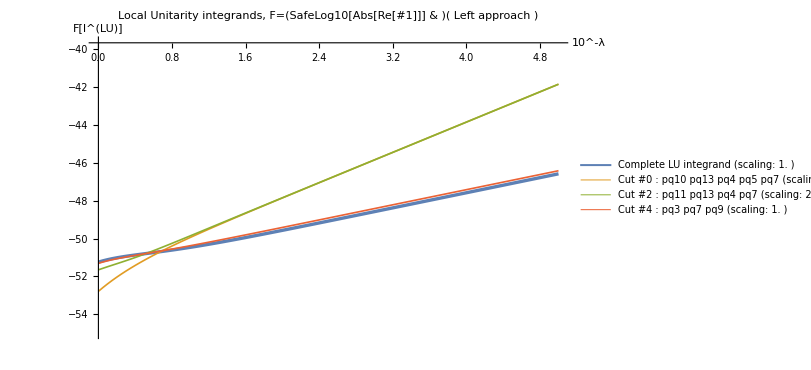
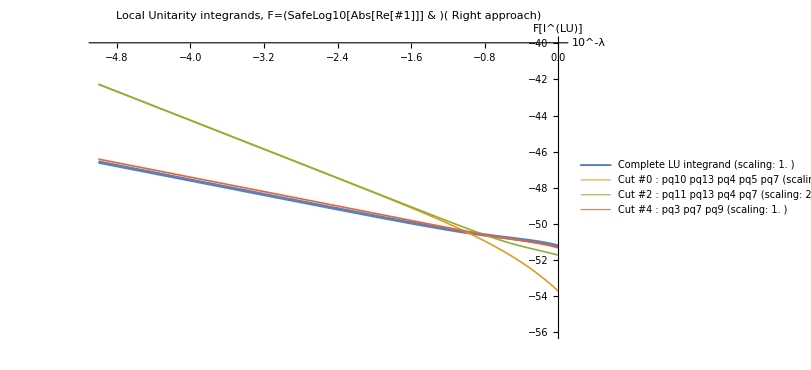
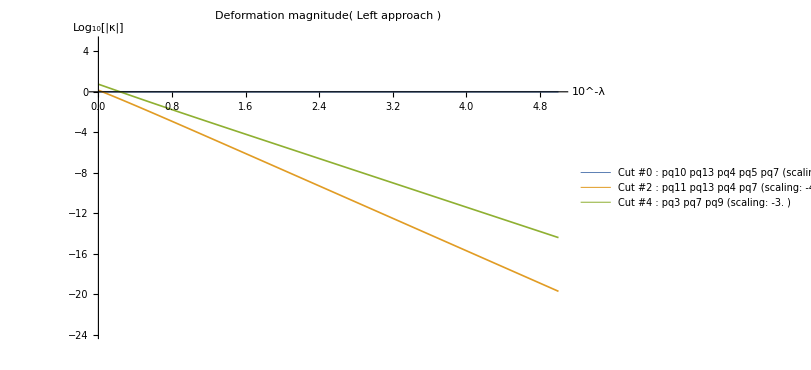
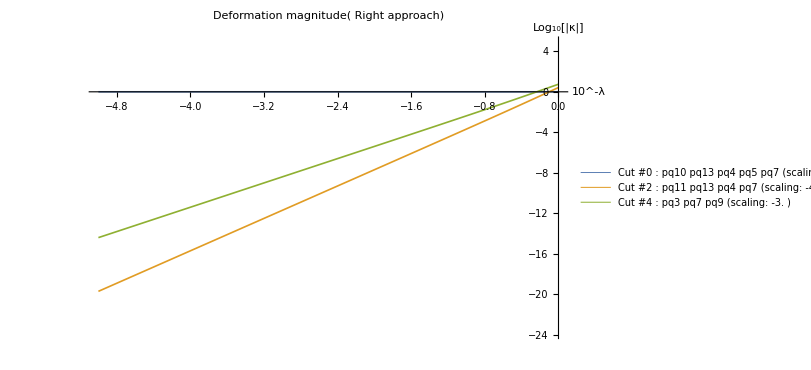
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[DoubleSidedMonitor[DoubleSidedApproachData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},IntegrandToPlot->(SafeLog10[Abs[Re[#]]]&)]]
```

### Study of approach of (intersections of) thresholds

We can display the supergraph

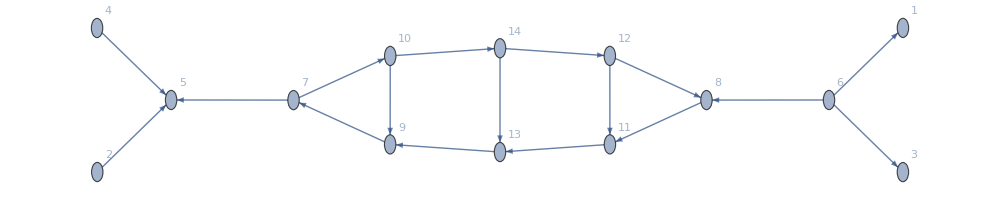

```mathematica
GetSuperGraph[SGYAMLinfo,ShowVertexLabels->Automatic,Size->1000]
```

And all of its LMBs, of which we show here the first twelve

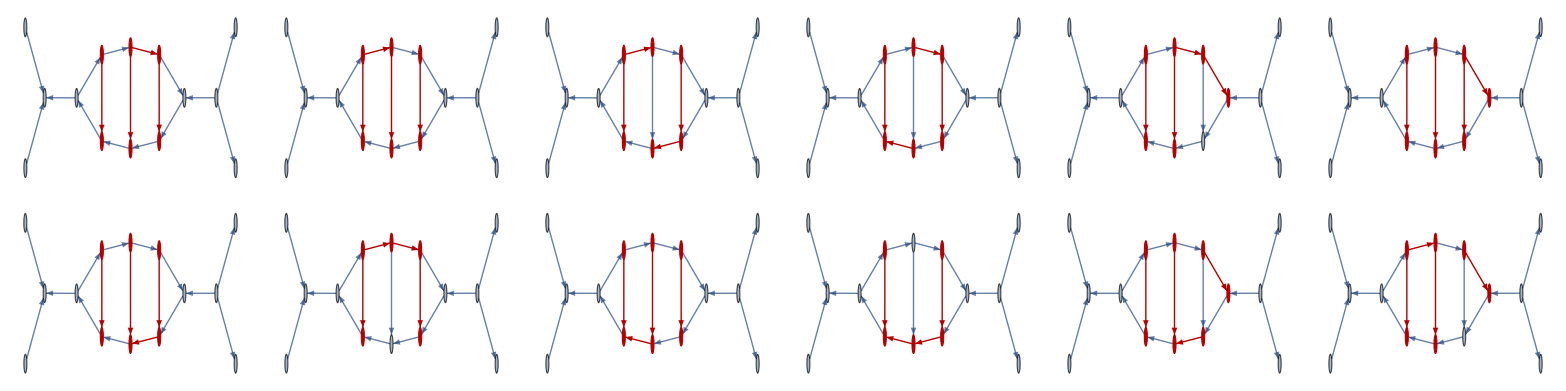

```mathematica
Table[HighlightGraph[GetSuperGraph[SGYAMLinfo],lmb],{lmb, GenerateAllLMBs[SGYAMLinfo]⟦;;12⟧}]//Multicolumn[#,6]&
```

We can automatically generate all E-surfaces (the only slow part is finding whether or not points exists on them)

```mathematica
allESurfaces=GenerateAllSGEsurfaces[SGYAMLinfo,paramsYaml->NoDeformationHyperparams,QuietMode->True,GenerateExamplePoints->True,AcceptThreshold->10^-20];
```

And display them:

All 16 s-channel E-surfaces:

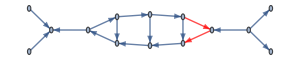
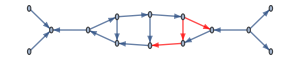
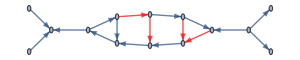
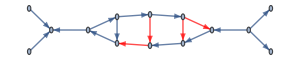
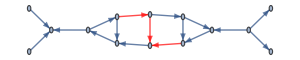
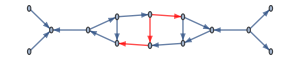
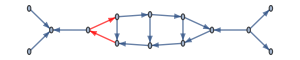
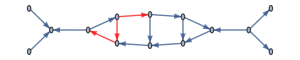
ID 1: | -Graphics- | ID 4: | -Graphics- | ID 7: | -Graphics- | ID 10: | -Graphics- | ID 13: | -Graphics- | ID 16: | -Graphics-
ID 2: | -Graphics- | ID 5: | -Graphics- | ID 8: | -Graphics- | ID 11: | -Graphics- | ID 14: | -Graphics- | 
ID 3: | -Graphics- | ID 6: | -Graphics- | ID 9: | -Graphics- | ID 12: | -Graphics- | ID 15: | -Graphics- |

All 12 soft E-surfaces:

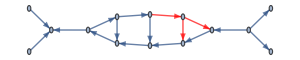
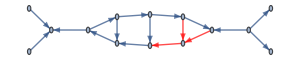
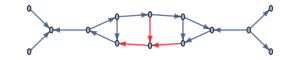
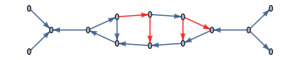
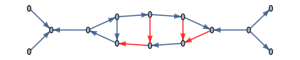
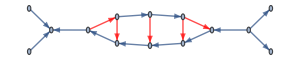
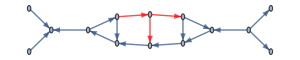
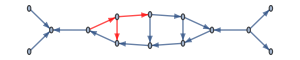
ID 1: | -Graphics- | ID 3: | -Graphics- | ID 5: | -Graphics- | ID 7: | -Graphics- | ID 9: | -Graphics- | ID 11: | -Graphics-
ID 2: | -Graphics- | ID 4: | -Graphics- | ID 6: | -Graphics- | ID 8: | -Graphics- | ID 10: | -Graphics- | ID 12: | -Graphics-

All 26 internal E-surfaces:

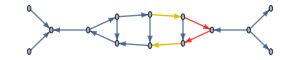
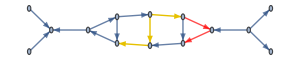
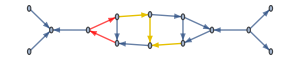
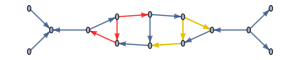
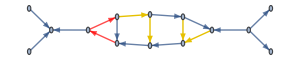
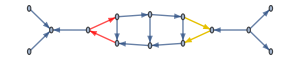
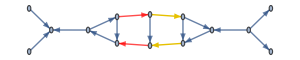
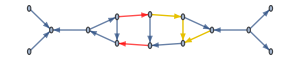
ID 1: | -Graphics- | ID 6: | -Graphics- | ID 11: | -Graphics- | ID 16: | -Graphics- | ID 21: | -Graphics- | ID 26: | -Graphics-
ID 2: | -Graphics- | ID 7: | -Graphics- | ID 12: | -Graphics- | ID 17: | -Graphics- | ID 22: | -Graphics- | 
ID 3: | -Graphics- | ID 8: | -Graphics- | ID 13: | -Graphics- | ID 18: | -Graphics- | ID 23: | -Graphics- | 
ID 4: | -Graphics- | ID 9: | -Graphics- | ID 14: | -Graphics- | ID 19: | -Graphics- | ID 24: | -Graphics- | 
ID 5: | -Graphics- | ID 10: | -Graphics- | ID 15: | -Graphics- | ID 20: | -Graphics- | ID 25: | -Graphics- |

All 30 composite E-surfaces:

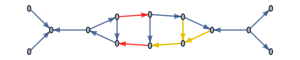
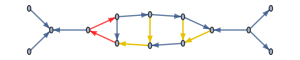
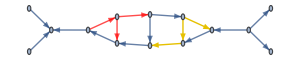
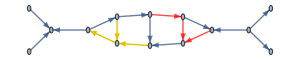
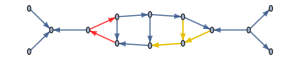
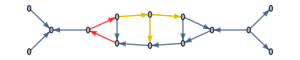
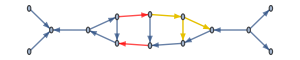
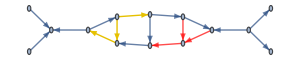
ID 1: | -Graphics- | ID 6: | -Graphics- | ID 11: | -Graphics- | ID 16: | -Graphics- | ID 21: | -Graphics- | ID 26: | -Graphics-
ID 2: | -Graphics- | ID 7: | -Graphics- | ID 12: | -Graphics- | ID 17: | -Graphics- | ID 22: | -Graphics- | ID 27: | -Graphics-
ID 3: | -Graphics- | ID 8: | -Graphics- | ID 13: | -Graphics- | ID 18: | -Graphics- | ID 23: | -Graphics- | ID 28: | -Graphics-
ID 4: | -Graphics- | ID 9: | -Graphics- | ID 14: | -Graphics- | ID 19: | -Graphics- | ID 24: | -Graphics- | ID 29: | -Graphics-
ID 5: | -Graphics- | ID 10: | -Graphics- | ID 15: | -Graphics- | ID 20: | -Graphics- | ID 25: | -Graphics- | ID 30: | -Graphics-

```mathematica
DisplayESurfaces[SGYAMLinfo,allESurfaces,Size->300,Colors->{Red}]
```

Or just one particular one

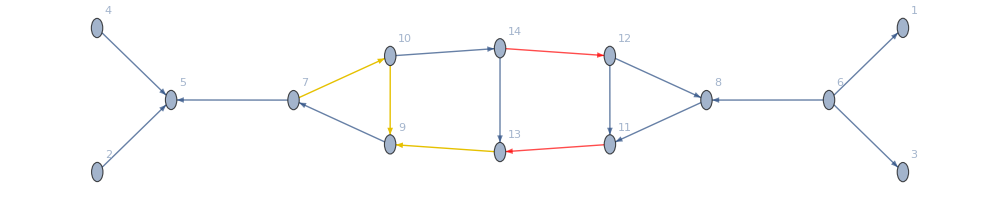

```mathematica
DisplayESurface[SGYAMLinfo,allESurfaces["internal"]⟦8⟧,Size->1000,Colors->{Red},ShowVertexLabels->Automatic]
```

And access a wealth of information about each, e.g.:

```mathematica
MyDataset[allESurfaces["internal"]⟦8⟧]
```

We can build a helper association to directly access Cutkosky cut E-surfaces.

```mathematica
AllCutkoskyEsurfaces=Association[Table[es["OutgoingEdges"]->es,{es,allESurfaces["s-channel"]}]];
```

And easily find a point on (multiple) E-surfaces as follows:

```mathematica
aPointToExplore=FindPointOnEsurfaces[{AllCutkoskyEsurfaces[{"pq3","pq7","pq9"}],AllCutkoskyEsurfaces[{"pq11","pq12"}],AllCutkoskyEsurfaces[{"pq5","pq6"}]},SGYAMLinfo,NoDeformationHyperparams,DEBUG->False,AcceptThreshold->10^-25]
```

<|pq4→{-140.647769214788576277944953,226.905642161317463997915286,-106.17444717912766226643494},pq7→{36.879637138344048350088657,-149.640028882297578919234924,11.3300236659390749409487173},pq10→{8.68427685049327694760774678,20.7275104815979656250317211,28.09209640779147151925579},pq13→{138.992613387962336599552544,51.4001383644170771960933069,1.51846678401996723689086769}|>

And we can verify that it is indeed located on these three E-surfaces

```mathematica
MyDataset[Association[Table[e->AllCutkoskyEsurfaces[e]["Eq"]/.GenerateLoopMomenta[SGYAMLinfo,moms->aPointToExplore],{e,Keys[AllCutkoskyEsurfaces]}]]]
```

Look at all momenta for this configuration:

```mathematica
ComputeAllMomenta[aPointToExplore,SGYAMLinfo,NoDeformationHyperparams,DatasetOutput->True]
```

Evaluate the LU expression on it, first without E-surface analysis:

```mathematica
MyDataset[EvaluatePoint[HookWithDeformation,aPointToExplore,SGYAMLinfo,NoDeformationHyperparams,
DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,Seed->1
]]
```

And then including the E-surface analysis

```mathematica
evaluationWithEsurfaceAnalysis=EvaluatePoint[HookWithDeformation,aPointToExplore,SGYAMLinfo,NoDeformationHyperparams,
DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,Seed->1,Esurfaces->allESurfaces
];
```

```mathematica
MyDataset[evaluationWithEsurfaceAnalysis]
```

And now with more detailed info about the E-surface analysis

```mathematica
DisplayEvaluationEsurf[evaluationWithEsurfaceAnalysis,SGYAMLinfo,Categories->{"s-channel","soft"}];
```

--------------------------------------------------

Analysis of s-channel E-surfaces:

--------------------------------------------------

Cut #0 | {pq10,pq13,pq4,pq5,pq7}
 | Cut #3 | {pq12,pq13,pq3,pq7}

Cut #1 | {pq10,pq13,pq3,pq6,pq7}
 | Cut #4 | {pq3,pq7,pq9}

Cut #2 | {pq11,pq13,pq4,pq7}
 | Cut #5 | {pq4,pq7,pq8}

--------------------------------------------------

Analysis of soft E-surfaces:

--------------------------------------------------

Cut #0 | {pq10,pq13,pq4,pq5,pq7}
 | Cut #3 | {pq12,pq13,pq3,pq7}

Cut #1 | {pq10,pq13,pq3,pq6,pq7}
 | Cut #4 | {pq3,pq7,pq9}

Cut #2 | {pq11,pq13,pq4,pq7}
 | Cut #5 | {pq4,pq7,pq8}

We can now approach this point automatically in a double-sided fashion with:

```mathematica
RefreshHooks[];
DoubleSidedApproachData=DoubleSidedApproach[HookWithDeformation,aPointToExplore,SGYAMLinfo,WithDeformationHyperparams,NPoints->100,Seed->1, LambdaMax->5.,LambdaMin->0];
```

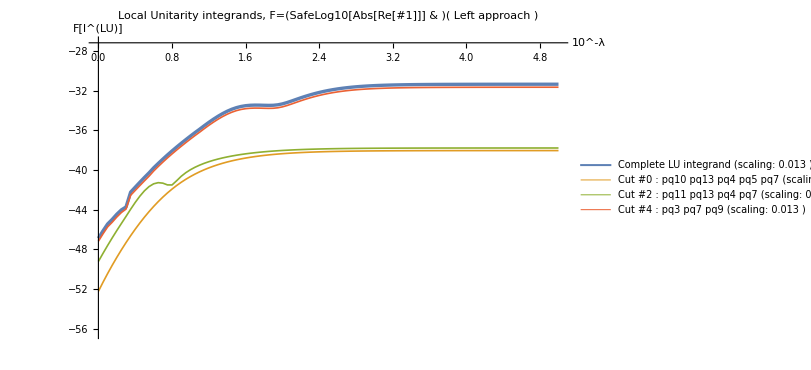
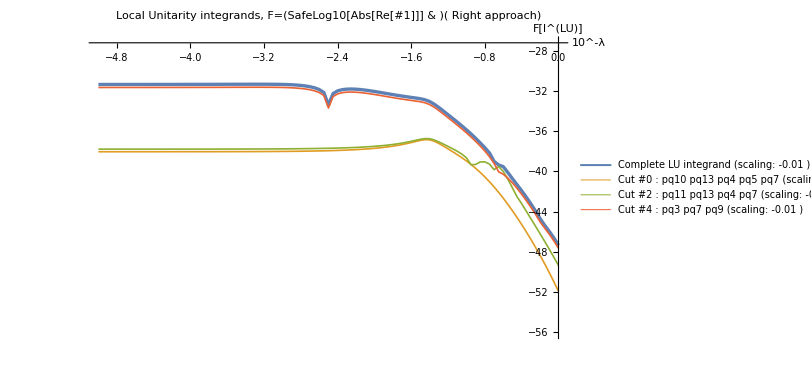
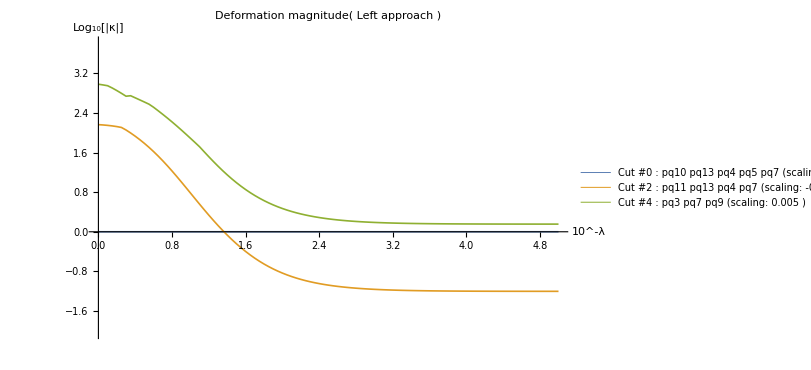
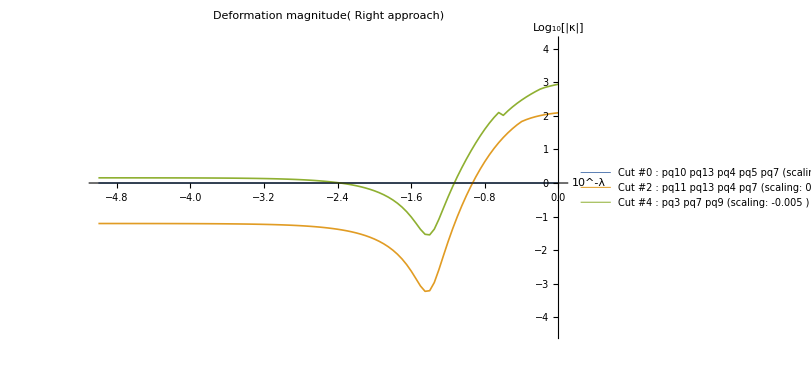
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[DoubleSidedMonitor[DoubleSidedApproachData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},IntegrandToPlot->(SafeLog10[Abs[Re[#]]]&)]]
```

But it sometimes better to not look in Log Log plot and study separately the real and imaginary part of the integrand

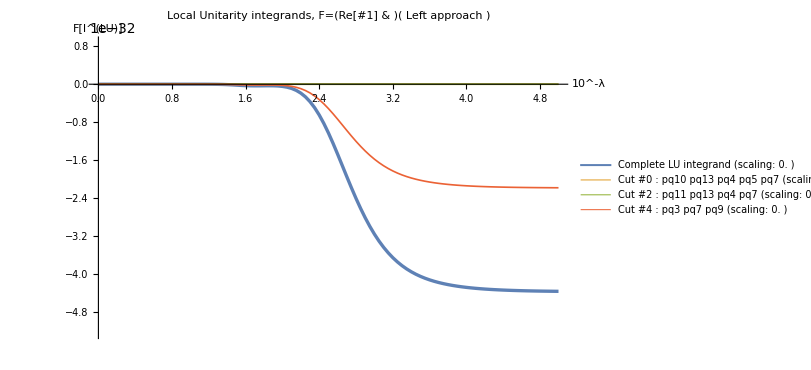
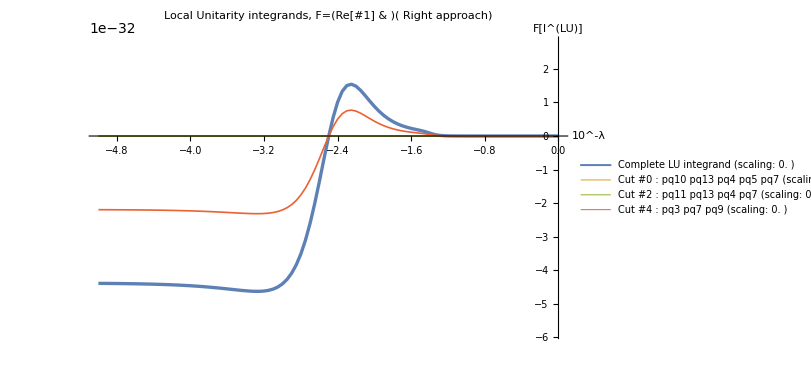
-Graphics- | -Graphics-

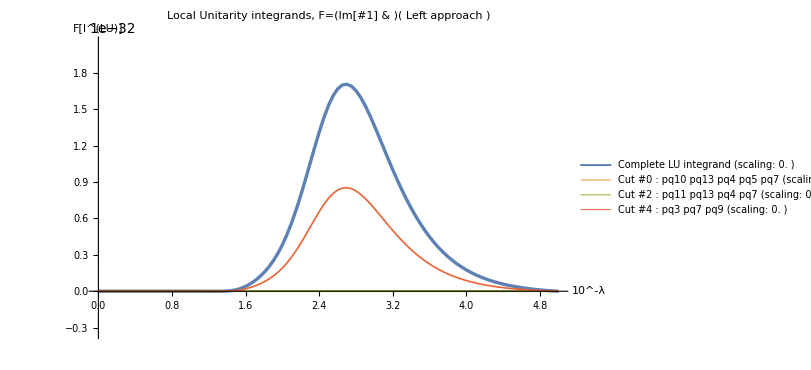
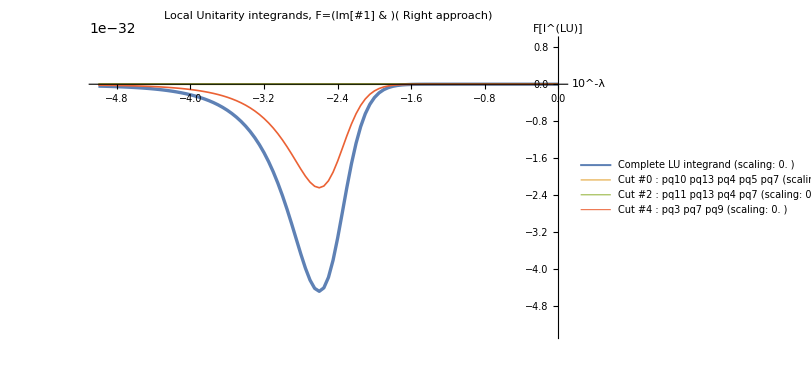
-Graphics- | -Graphics-

```mathematica
Grid[{DoubleSidedMonitor[DoubleSidedApproachData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},IntegrandToPlot->(Re[#]&)]⟦1⟧}]
Grid[{DoubleSidedMonitor[DoubleSidedApproachData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},IntegrandToPlot->(Im[#]&)]⟦1⟧}]
```

And one can bypass the double-sided study and just directly look at a single approach

```mathematica
RefreshHooks[];
ApproachRawData=AnalyzeApproach[HookWithDeformation,aPointToExplore,SGYAMLinfo,WithDeformationHyperparams,NPoints->300,Seed->1, LambdaMax->5.,LambdaMin->0,ApproachSide->-1];
```

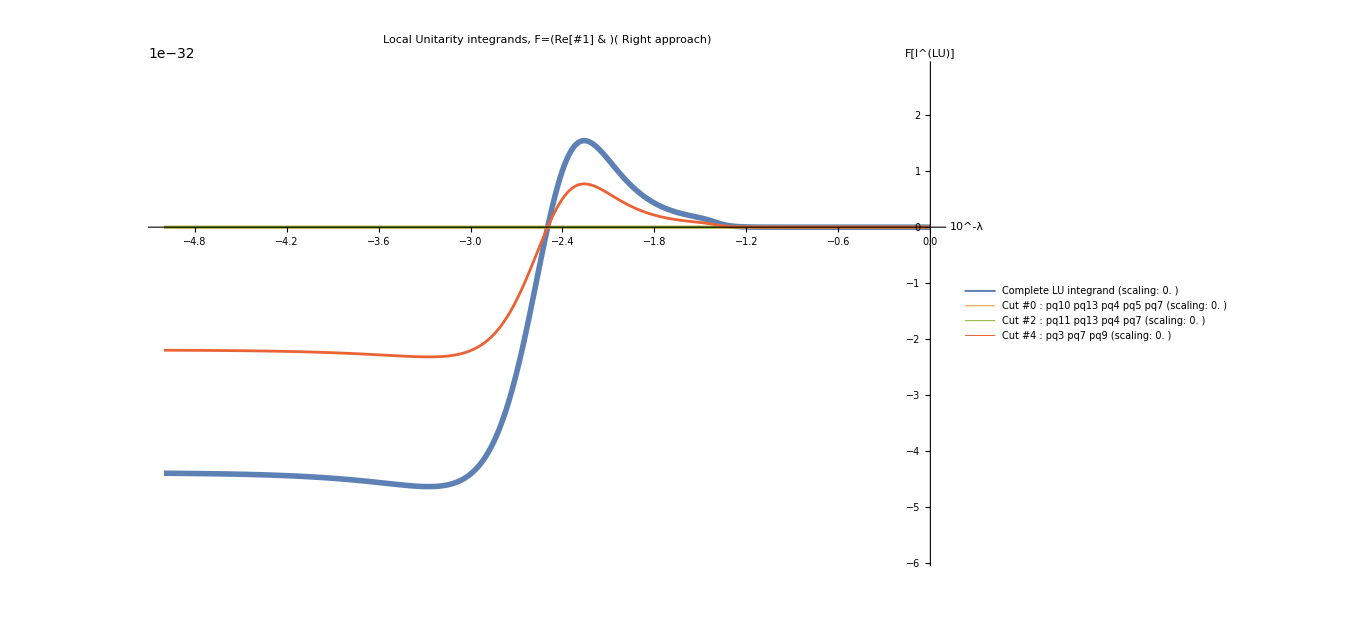
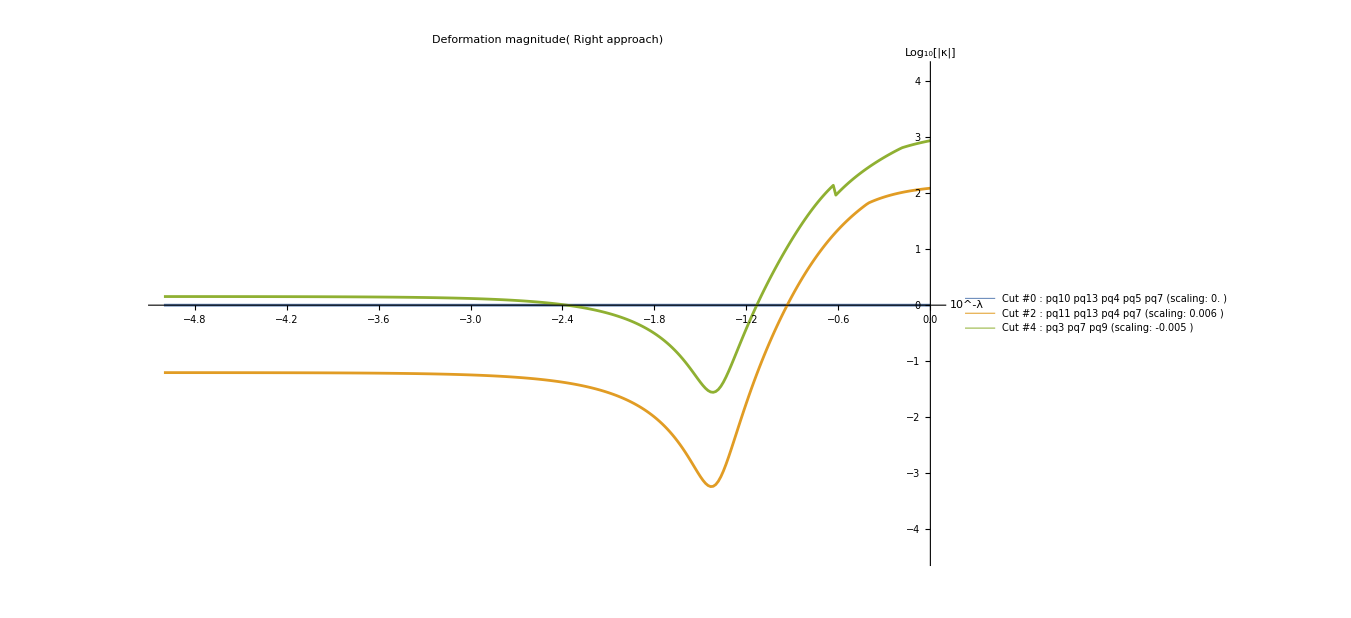

```mathematica
Grid[MonitorApproachResult[ApproachRawData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},ApproachSide->-1,IntegrandToPlot->(Re[#]&)]]
```

### Analysis of a max weight point

We can automatically map the xs variable to the point in the sampling basis active at run time (use all integration channels if multichanneling was enabled

```mathematica
maxWgtPoint=MapFromXs[HookWithDeformation,
{0.849593720848453,0.24429579449322847,0.6402108135745326,0.8560665730509239,0.7384368123709596,0.36724149939496614,0.14036138814108864,0.16762193841514772,0.6144196438490055,0.34658379011798746,0.16176951799648479,0.7382519129987205}, 
SGYAMLinfo,NoDeformationHyperparams,basis->{"pq10", "pq13", "pq7", "pq5"}]
```

<|pq4→{102.169,234.105,294.913},pq7→{78.6458,138.126,37.3648},pq10→{194.287,5418.53,1584.01},pq13→{-416.242,-5719.04,-1579.2}|>

And now run the standard set of analysis tools onto it

```mathematica
ComputeAllMomenta[maxWgtPoint,SGYAMLinfo,NoDeformationHyperparams,DatasetOutput->True]
```

```mathematica
evaluationWithEsurfaceAnalysis=EvaluatePoint[HookWithDeformation,maxWgtPoint,SGYAMLinfo,NoDeformationHyperparams,
DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,Seed->1,Esurfaces->allESurfaces
];
```

```mathematica
Dataset[evaluationWithEsurfaceAnalysis][All,"Rescaling"]
```

```mathematica
DisplayEvaluationEsurf[evaluationWithEsurfaceAnalysis,SGYAMLinfo,Categories->{"s-channel"}];
```

--------------------------------------------------

Analysis of s-channel E-surfaces:

--------------------------------------------------

Cut #0 | {pq10,pq13,pq4,pq5,pq7}
 | Cut #3 | {pq12,pq13,pq3,pq7}

Cut #1 | {pq10,pq13,pq3,pq6,pq7}
 | Cut #4 | {pq3,pq7,pq9}

Cut #2 | {pq11,pq13,pq4,pq7}
 | Cut #5 | {pq4,pq7,pq8}

```mathematica
RefreshHooks[];
DoubleSidedApproachData=DoubleSidedApproach[HookWithDeformation,maxWgtPoint,SGYAMLinfo,WithDeformationHyperparams,NPoints->100,Seed->1, LambdaMax->5.,LambdaMin->0];
```

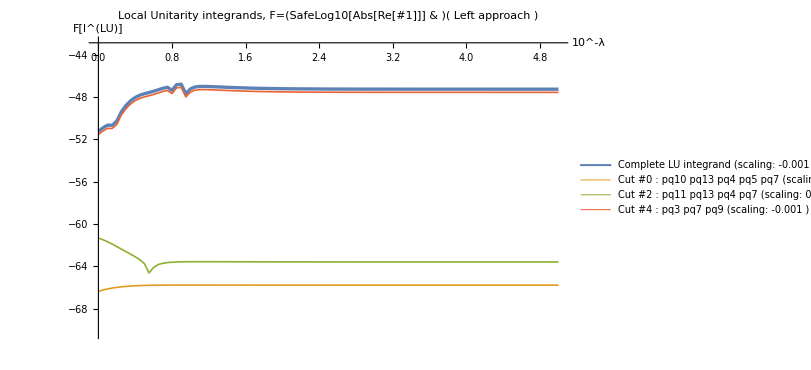
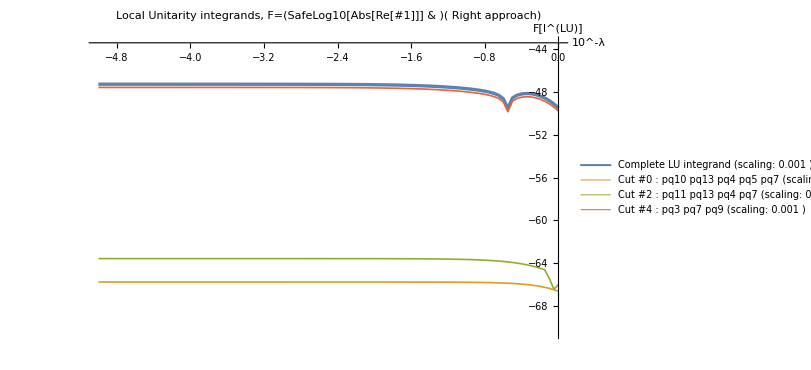
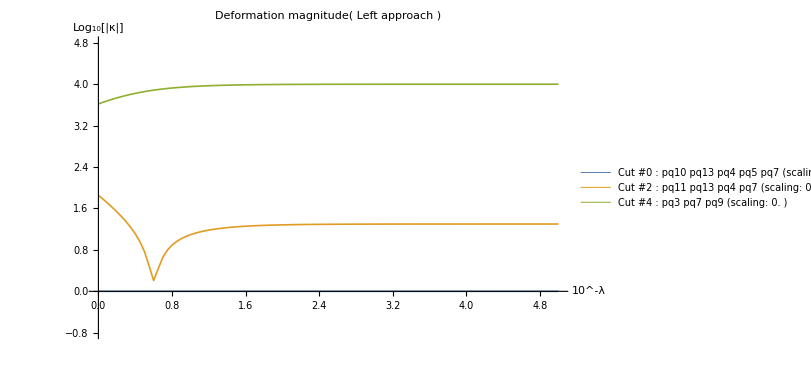
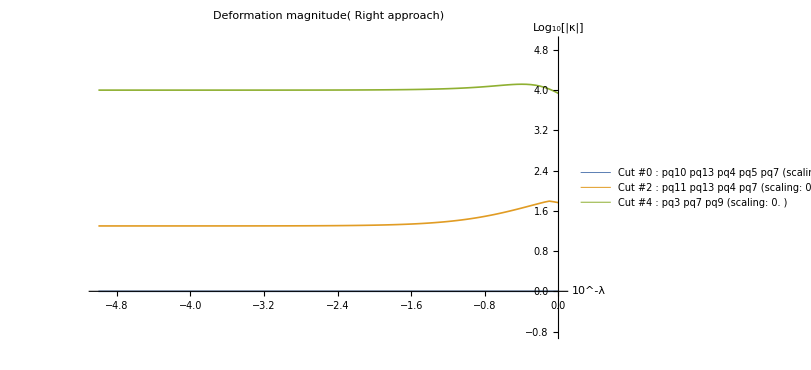
-Graphics- | -Graphics-
-Graphics- | -Graphics-

```mathematica
Grid[DoubleSidedMonitor[DoubleSidedApproachData,SGYAMLinfo,WithDeformationHyperparams,cuts->{-1,0,2,4},IntegrandToPlot->(SafeLog10[Abs[Re[#]]]&)]]
```

### Workspace

```mathematica
workspacePoint=FindPointOnEsurfaces[{AllCutkoskyEsurfaces[{"pq4","pq7","pq11","pq13"}],AllCutkoskyEsurfaces[{"pq5","pq9","pq10","pq13"}]},SGYAMLinfo,NoDeformationHyperparams,DEBUG->False,AcceptThreshold->10^-25]
```

<|pq4→{107.613324534007618715895301,-45.9796752912493394566852276,21.6110252266800466124289769},pq7→{-10.7605102416192759031303062,30.8533310266359021088324808,-87.4699590591587008096499243},pq10→{-56.3605502114347538272018378,79.8639013654874227916990731,-12.36466326999227768137983},pq13→{-71.7688976006418493058968915,-216.6509049899425665398213,-124.133653866270017988054949}|>

```mathematica
evaluationWithEsurfaceAnalysis=EvaluatePoint[HookWithDeformation,workspacePoint,SGYAMLinfo,NoDeformationHyperparams,
DEBUG->False,f128->True,IncludeJacobian->False,Phase->Null,Seed->1,Esurfaces->allESurfaces
];
DisplayEvaluationEsurf[evaluationWithEsurfaceAnalysis,SGYAMLinfo,Categories->{"s-channel"}];
MyDataset[evaluationWithEsurfaceAnalysis]
```

--------------------------------------------------

Analysis of s-channel E-surfaces:

--------------------------------------------------

Cut #0 | {pq10,pq13,pq4,pq5,pq7}
 | Cut #3 | {pq12,pq13,pq3,pq7}

Cut #1 | {pq10,pq13,pq3,pq6,pq7}
 | Cut #4 | {pq3,pq7,pq9}

Cut #2 | {pq11,pq13,pq4,pq7}
 | Cut #5 | {pq4,pq7,pq8}